## VO2 temperature transformation

#### Import data

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b"]
vo2Data=ReadList["allBands.out",Table[Number,{i,1,23}]];
Tc=340.65;
T0=329.65;
Tfrac=(Tc-T0)/Tc;
omega0R=-10.7507508144;
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
vo2Data[[1]]
```

{1,0.,0.,0.5,-6.05776,-6.05776,4.73051,4.73051,6.92554,6.92554,7.48591,7.48591,8.60587,8.60587,12.398,12.398,13.0901,13.0901,15.2323,15.2323,18.3013,0.0333687,1.}

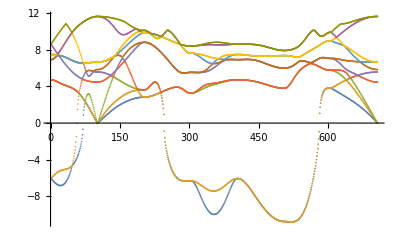

```mathematica
originalBandi[i_]:=Transpose@{Transpose[vo2Data][[1]],Transpose[vo2Data][[4+i]]}
ListPlot@Table[originalBandi[i],{i,1,10}]
```

#### Transformation functions

```mathematica
(*Define linear or FD shift function*)
tFunction[arg_,beta_,mu_]:=1/(Exp[-beta*(arg/0.5-mu)]+1)
tFunctionLin[arg_,beta_,mu_]:=arg/0.5
tFunctionPiece[arg_]:=If[arg==0,1,If[arg/0.5==1,1,0]]
```

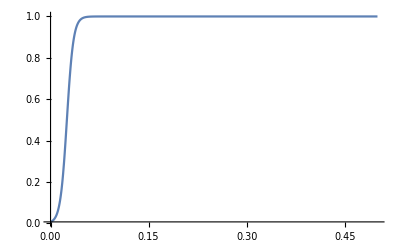

```mathematica
Plot[tFunction[arg,100,0.05],{arg,0,0.5},PlotRange->All]
```

#### Select the transition bands by hand

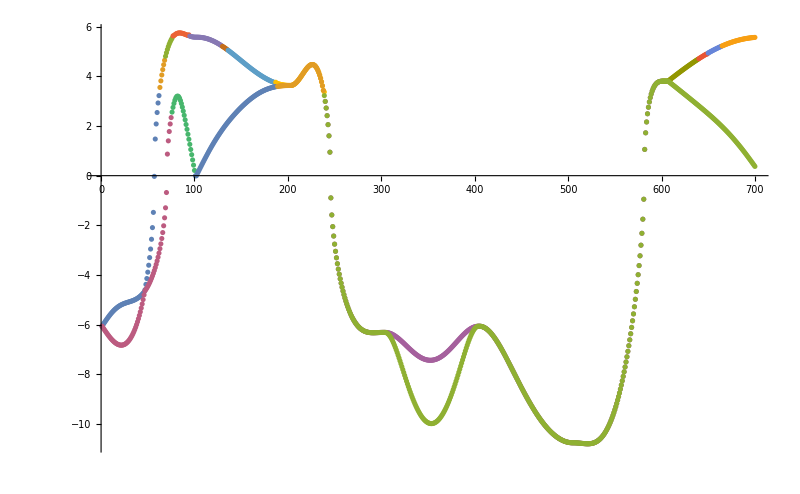

```mathematica
l1={originalBandi[1][[1;;75]],originalBandi[3][[76;;100]],originalBandi[2][[101;;188]],originalBandi[3][[189;;238]],originalBandi[1][[239;;700]]};
l2={originalBandi[2][[1;;62]],originalBandi[4][[63;;68]],originalBandi[5][[69;;76]],originalBandi[6][[77;;94]],originalBandi[5][[95;;129]],originalBandi[4][[130;;135]],originalBandi[3][[136;;186]],originalBandi[4][[187;;239]],originalBandi[2][[240;;600]],originalBandi[2][[601;;639]],originalBandi[3][[640;;649]],originalBandi[4][[650;;664]],originalBandi[5][[665;;700]]};
ListPlot[Join@@{l2,l1},ImageSize->800,PlotRange->All]
```

#### Apply the Fermi-Dirac type transformation

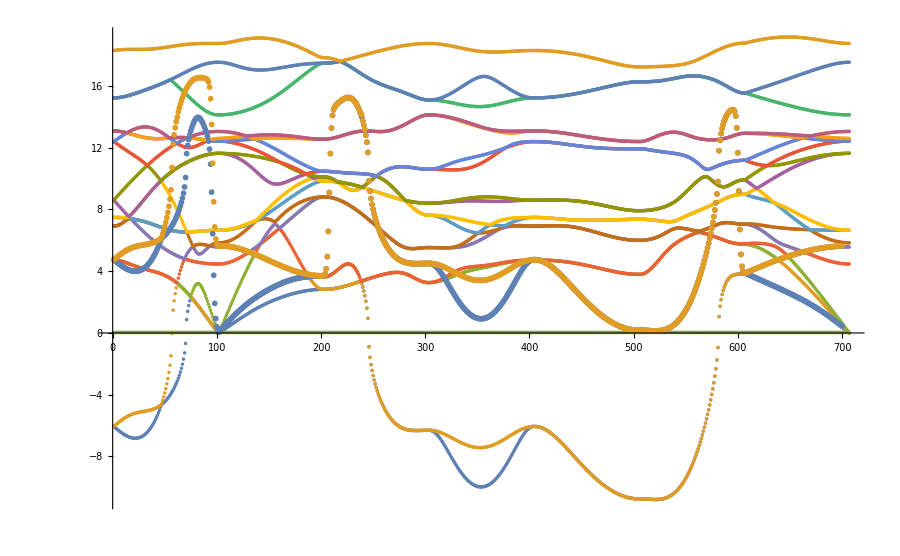

```mathematica
(*Set the value of the parameters for the interpolation*)
With[{mu=0.01*5,beta=100,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

## Force constant Hessian matrix

```mathematica
listFCvo2=ReadList["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b/FCnew",Number];
```

```mathematica
(*3natoms = 3*2*2*3*6=216*)
```

```mathematica
listFCvo2//Dimensions
listFCvo2Part=Partition[listFCvo2,216];
```

{46656}

```mathematica
ilistFCvo2Part=Inverse[listFCvo2Part]
```

{{-501532.,47.3702,-0.000038852,-501547.,46.2932,-0.000038853,-501548.,46.2915,-0.0000388524,-501542.,46.854,-0.0000388524,-501546.,47.8893,188,-23.9353,-0.27702,-501792.,-23.6598,-0.500605,-501793.,-24.6465,0.205632,-501793.,-24.8564,0.010278,-501793.,-23.9353,0.276942},214,{1}}
 |  |  |  |

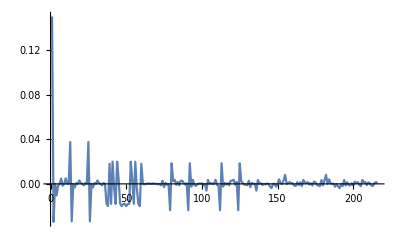

```mathematica
(*Row 1 of the Hessian*)
ListLinePlot[listFCvo2Part[[1]],PlotRange->All]
```

```mathematica
(*The sum rule is more or less satisfied - translational invariance*)
Table[Total@listFCvo2Part[[i]],{i,1,Length@listFCvo2Part}][[1;;10]]
```

{-4.15249×10^-8,-4.15249×10^-8,-4.85723×10^-17,-4.15249×10^-8,-4.15249×10^-8,-5.55112×10^-17,-4.15249×10^-8,-4.15249×10^-8,-4.85723×10^-17,-4.15249×10^-8}

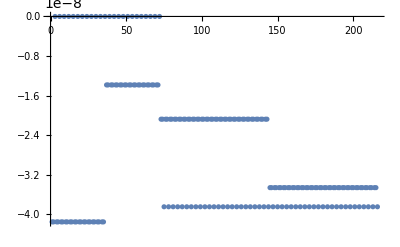

```mathematica
ListPlot@Table[Total@listFCvo2Part[[i]],{i,1,Length@listFCvo2Part}]
```

## Exact transformation at q_z=0 and q_z=0.5 + Gaussian interpolation for 0<q_z<0.5

#### Apply the transition only at q_z=0.5, setting it to zero for 0<q_z<0.5

```mathematica
(*Note, the bits set to zero are deleted to remove those data points*)
transformedBandA=Join[Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,95,100}],DeleteCases[Table[{Transpose[Join@@l1][[1]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l1][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,2,700}],x_/;x[[2]]<0.00010]];
transformedBandB=DeleteCases[Table[{Transpose[Join@@l2][[1]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l2][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}],x_/;x[[2]]<0.000010];
```

```mathematica
Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,90,100}]
```

{{90,2.24679},{91,2.05884},{92,1.86518},{93,1.66701},{94,1.46524},{95,1.26058},{96,1.05365},{97,0.844914},{98,0.634815},{99,0.423722},{100,0.211963}}

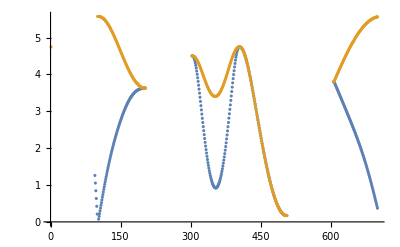

```mathematica
ListPlot@Join@{transformedBandA,transformedBandB}
```

#### Get data to train Gaussian process ML interpolation

Make the initial data set like {index,qz,qy,qz,transformationBandEnergy}

```mathematica
vo2Data[[90;;110]]//TableForm
```

90 | 0. | 0. | 0.055 | 1.04019 | 1.04019 | 2.24679 | 4.5038 | 5.43771 | 5.68859 | 6.6246 | 6.6246 | 11.5407 | 11.5407 | 12.4223 | 12.4949 | 12.4949 | 12.9964 | 14.3637 | 17.446 | 18.7564 | 0.0333687 | 0.11
91 | 0. | 0. | 0.05 | 0.947226 | 0.947226 | 2.05884 | 4.49769 | 5.50107 | 5.67329 | 6.62886 | 6.62886 | 11.5568 | 11.5568 | 12.4515 | 12.4859 | 12.4859 | 13.0068 | 14.3254 | 17.4619 | 18.7567 | 0.0333687 | 0.1
92 | 0. | 0. | 0.045 | 0.853798 | 0.853798 | 1.86518 | 4.4922 | 5.56121 | 5.65783 | 6.63281 | 6.63281 | 11.5717 | 11.5717 | 12.4773 | 12.4773 | 12.4788 | 13.0162 | 14.2901 | 17.4763 | 18.7568 | 0.0333687 | 0.09
93 | 0. | 0. | 0.04 | 0.759956 | 0.759956 | 1.66701 | 4.48732 | 5.61704 | 5.64267 | 6.63644 | 6.63644 | 11.5852 | 11.5852 | 12.4692 | 12.4692 | 12.504 | 13.0246 | 14.258 | 17.4894 | 18.7569 | 0.0333687 | 0.08
94 | 0. | 0. | 0.035 | 0.665748 | 0.665748 | 1.46524 | 4.48304 | 5.62826 | 5.66776 | 6.63969 | 6.63969 | 11.5973 | 11.5973 | 12.4619 | 12.4619 | 12.5268 | 13.032 | 14.2292 | 17.5009 | 18.7569 | 0.0333687 | 0.07
95 | 0. | 0. | 0.03 | 0.571221 | 0.571221 | 1.26058 | 4.47935 | 5.61497 | 5.71273 | 6.64257 | 6.64257 | 11.608 | 11.608 | 12.4553 | 12.4553 | 12.547 | 13.0385 | 14.204 | 17.511 | 18.7568 | 0.0333687 | 0.06
96 | 0. | 0. | 0.025 | 0.476421 | 0.476421 | 1.05365 | 4.47624 | 5.60315 | 5.75147 | 6.64503 | 6.64503 | 11.6172 | 11.6172 | 12.4495 | 12.4495 | 12.5644 | 13.0439 | 14.1824 | 17.5195 | 18.7568 | 0.0333687 | 0.05
97 | 0. | 0. | 0.02 | 0.381394 | 0.381394 | 0.844914 | 4.47371 | 5.59308 | 5.78363 | 6.64708 | 6.64708 | 11.6248 | 11.6248 | 12.4447 | 12.4447 | 12.5789 | 13.0484 | 14.1645 | 17.5265 | 18.7567 | 0.0333687 | 0.04
98 | 0. | 0. | 0.015 | 0.286183 | 0.286183 | 0.634815 | 4.47175 | 5.585 | 5.8089 | 6.64868 | 6.64868 | 11.6308 | 11.6308 | 12.4409 | 12.4409 | 12.5903 | 13.0518 | 14.1505 | 17.532 | 18.7566 | 0.0333687 | 0.03
99 | 0. | 0. | 0.01 | 0.190827 | 0.190827 | 0.423722 | 4.47035 | 5.57909 | 5.8271 | 6.64983 | 6.64983 | 11.6351 | 11.6351 | 12.4381 | 12.4381 | 12.5985 | 13.0543 | 14.1405 | 17.5359 | 18.7565 | 0.0333687 | 0.02
100 | 0. | 0. | 0.005 | 0.0953377 | 0.0953377 | 0.211963 | 4.46951 | 5.5755 | 5.83808 | 6.65053 | 6.65053 | 11.6377 | 11.6377 | 12.4364 | 12.4364 | 12.6034 | 13.0558 | 14.1344 | 17.5383 | 18.7565 | 0.0333687 | 0.01
101 | 0. | 0. | 0. | -0.00563432 | -0.004994 | -0.004994 | 4.46923 | 5.57429 | 5.84174 | 6.65076 | 6.65076 | 11.6386 | 11.6386 | 12.4359 | 12.4359 | 12.6051 | 13.0563 | 14.1324 | 17.5391 | 18.7565 | 0.0333687 | 0
102 | 0. | 0. | 0. | -0.00563432 | -0.004994 | -0.004994 | 4.46923 | 5.57429 | 5.84174 | 6.65076 | 6.65076 | 11.6386 | 11.6386 | 12.4359 | 12.4359 | 12.6051 | 13.0563 | 14.1324 | 17.5391 | 18.7565 | 0.0333687 | 0
103 | 0.005 | 0.005 | 0. | 0.0457738 | 0.0753184 | 0.160066 | 4.47035 | 5.57388 | 5.84297 | 6.65122 | 6.6514 | 11.6377 | 11.6384 | 12.4351 | 12.436 | 12.6056 | 13.0558 | 14.1328 | 17.538 | 18.7573 | 0.0333687 | 0
104 | 0.01 | 0.01 | 0. | 0.0919578 | 0.150863 | 0.320192 | 4.4737 | 5.57265 | 5.84667 | 6.65258 | 6.6533 | 11.635 | 11.6379 | 12.4327 | 12.4365 | 12.6073 | 13.0545 | 14.1341 | 17.5347 | 18.7598 | 0.0333687 | 0
105 | 0.015 | 0.015 | 0. | 0.138056 | 0.226157 | 0.480182 | 4.47927 | 5.57057 | 5.85286 | 6.65486 | 6.65647 | 11.6305 | 11.6371 | 12.4287 | 12.4373 | 12.6099 | 13.0523 | 14.1363 | 17.5293 | 18.7639 | 0.0333687 | 0
106 | 0.02 | 0.02 | 0. | 0.184137 | 0.301167 | 0.639997 | 4.48705 | 5.56761 | 5.86158 | 6.65805 | 6.6609 | 11.6242 | 11.6359 | 12.4234 | 12.4384 | 12.6134 | 13.0492 | 14.1393 | 17.5219 | 18.7695 | 0.0333687 | 0
107 | 0.025 | 0.025 | 0. | 0.230216 | 0.375816 | 0.799586 | 4.497 | 5.56371 | 5.87285 | 6.66217 | 6.66659 | 11.6162 | 11.6344 | 12.4168 | 12.4398 | 12.6177 | 13.0453 | 14.1432 | 17.5125 | 18.7766 | 0.0333687 | 0
108 | 0.03 | 0.03 | 0. | 0.276295 | 0.450025 | 0.958895 | 4.5091 | 5.55885 | 5.88671 | 6.66721 | 6.67351 | 11.6063 | 11.6326 | 12.4091 | 12.4415 | 12.6226 | 13.0404 | 14.148 | 17.5013 | 18.785 | 0.0333687 | 0
109 | 0.035 | 0.035 | 0. | 0.322374 | 0.523715 | 1.11787 | 4.5233 | 5.55297 | 5.90319 | 6.67319 | 6.68167 | 11.5946 | 11.6304 | 12.4003 | 12.4436 | 12.628 | 13.0347 | 14.1536 | 17.4884 | 18.7947 | 0.0333687 | 0
110 | 0.04 | 0.04 | 0. | 0.368448 | 0.596809 | 1.27645 | 4.53956 | 5.54606 | 5.92228 | 6.68012 | 6.69104 | 11.581 | 11.6279 | 12.3906 | 12.4459 | 12.6339 | 13.0281 | 14.1601 | 17.4741 | 18.8054 | 0.0333687 | 0

```mathematica
transformedBandAq3=Join[Table[{Transpose[Join@@l1][[1]][[i]],Transpose[vo2Data][[2]][[i]],Transpose[vo2Data][[3]][[i]],Transpose[vo2Data][[4]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,95,100}],DeleteCases[Table[{Transpose[Join@@l1][[1]][[i]],Transpose[vo2Data][[2]][[i]],Transpose[vo2Data][[3]][[i]],Transpose[vo2Data][[4]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l1][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}],x_/;x[[5]]<0.00001]];
transformedBandBq3=DeleteCases[Table[{Transpose[Join@@l2][[1]][[i]],Transpose[vo2Data][[2]][[i]],Transpose[vo2Data][[3]][[i]],Transpose[vo2Data][[4]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l2][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}],x_/;x[[5]]<0.000001];
```

#### Make the training set

Map {qx,qy,qz}->{transformationBandEnergy} for all transformed bands in the following part of the BZ: 0<qx<0.5 AND 0<qy<0.5 AND (qz=0 OR qz=0.5)

```mathematica
mapDataA={Transpose@Transpose[transformedBandAq3][[2;;4]]->Transpose[transformedBandAq3][[5]]};
mapDataB={Transpose@Transpose[transformedBandBq3][[2;;4]]->Transpose[transformedBandBq3][[5]]};
```

#### Train model

```mathematica
modelA=Predict[mapDataA[[1]],Method->"GaussianProcess"]
modelB=Predict[mapDataB[[1]],Method->"GaussianProcess"]
```

PredictorFunction[…]

PredictorFunction[…]

#### Make plotable

```mathematica
qList=Transpose@{Transpose[vo2Data][[2]],Transpose[vo2Data][[3]],Transpose[vo2Data][[4]]};
newBandA=Table[{i,modelA[qList[[i]]]},{i,1,700}];
newBandB=Table[{i,modelB[qList[[i]]]},{i,1,700}];
```

#### Plot transformed bands with GP interpolation for 0<q_z<0.5

```mathematica
styleLegend[arg_]:=Style[ToString@arg,18]
```

```mathematica
labels={Style["i=1: {q_x,q_y,0<q_z<0.5} Gaussian interpolation",20,FontFamily->Times],Style["i=1: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform",20,FontFamily->Times],Style["i=2: {q_x,q_y,0<q_z<0.5} Gaussian interpolation",20,FontFamily->Times],Style["i=2: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform",20,FontFamily->Times]}
```

{i=1: {q_x,q_y,0<q_z<0.5} Gaussian interpolation,i=1: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform,i=2: {q_x,q_y,0<q_z<0.5} Gaussian interpolation,i=2: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform}

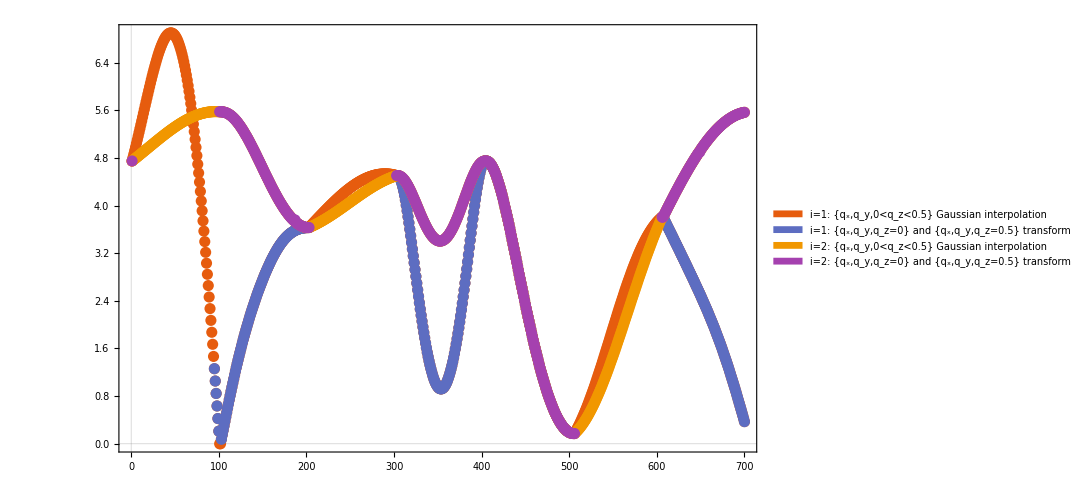

```mathematica
p1=ListPlot[Join@{newBandA,transformedBandA,newBandB,
transformedBandB},PlotRange->All,PlotStyle->Directive[PointSize[0.01],18],
PlotLegends->SwatchLegend@{labels},PlotTheme->"Scientific",ImageSize->800]
```

{50,0.,0.,0.255,-4.45239,-3.88347,3.72994,3.72994,5.44664,6.76361,6.76361,9.47111,10.0865,10.0865,11.7877,12.6071,12.6071,12.8565,16.2406,16.2406,18.4975,0.0333687,0.51}

{150,0.24,0.24,0.,1.98581,2.75016,4.62765,6.21104,6.62237,7.36422,7.79203,8.10285,9.78264,11.2546,11.4446,12.1377,12.6221,12.837,15.0751,17.068,19.0763,0.0333687,0}

{250,0.5,0.5,0.235,-2.75577,-2.75577,3.60621,3.60621,7.10434,7.10434,9.21833,9.21833,10.0008,10.0008,10.2209,10.2209,13.0672,13.0672,16.3457,16.3457,18.1711,0.0333687,0.47}

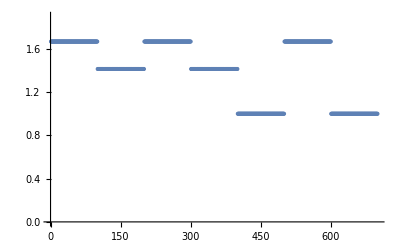

```mathematica
vo2Data[[50]]
vo2Data[[150]]
vo2Data[[250]]
cOVERa=1.668;
scaleFactors=Join[Table[cOVERa,{i,100}],Table[Sqrt[2],{i,100}],Table[cOVERa,{i,100}],Table[Sqrt[2],{i,100}],Table[1,{i,100}],Table[cOVERa,{i,100}],Table[1,{i,100}]];
ListPlot[scaleFactors,PlotRange->{Automatic,{0,1.9}}]
```

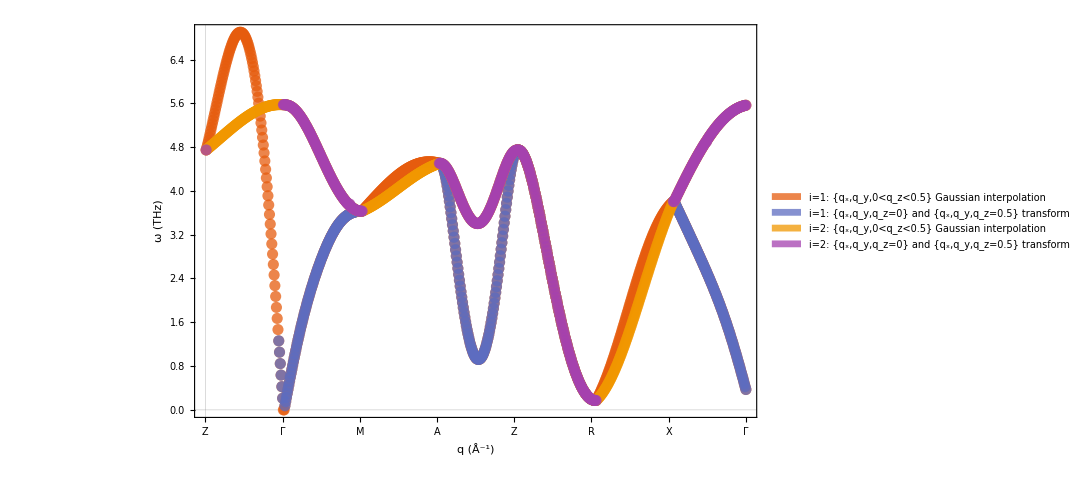

```mathematica
p1a=ListPlot[Join@{newBandA,transformedBandA,newBandB,
transformedBandB},PlotRange->All,FrameStyle->Directive[Black,18],FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific",FrameTicks->{{Automatic,None},{{{0,Style["Z",20]},{100,Style["Γ",20]},{200,Style["M",20]},{300,Style["A",20]},{400,Style["Z",20]},{500,Style["R",20]},{600,Style["X",20]},{700,Style["Γ",20]}},None}},PlotStyle->Directive[PointSize[0.01],18,Opacity[0.75]],
PlotLegends->SwatchLegend@{labels},PlotTheme->"Scientific",ImageSize->800]
```

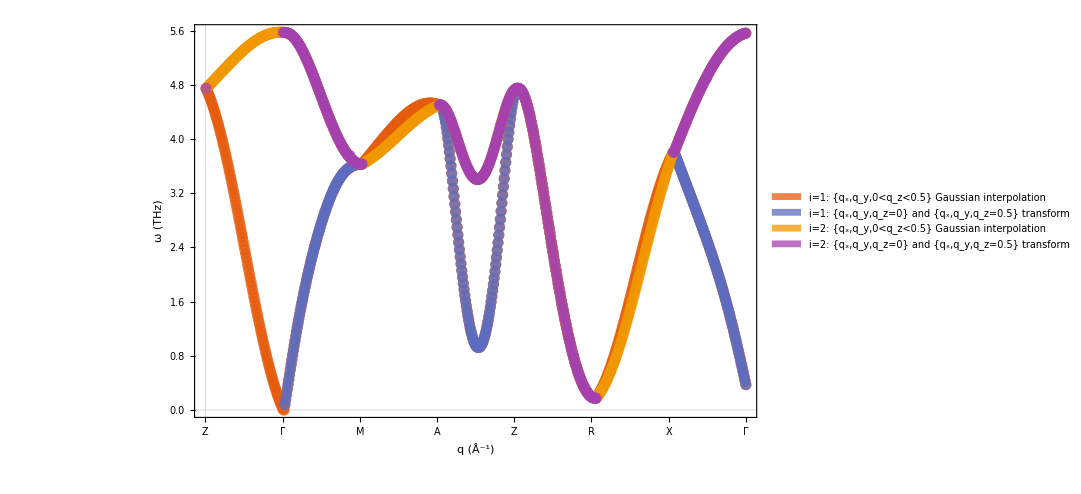

```mathematica
p1a=ListPlot[Join@{newBandA,transformedBandA,newBandB,
transformedBandB},PlotRange->All,FrameStyle->Directive[Black,18],FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific",FrameTicks->{{Automatic,None},{{{0,Style["Z",20]},{100,Style["Γ",20]},{200,Style["M",20]},{300,Style["A",20]},{400,Style["Z",20]},{500,Style["R",20]},{600,Style["X",20]},{700,Style["Γ",20]}},None}},PlotStyle->Directive[PointSize[0.01],18,Opacity[0.75]],
PlotLegends->SwatchLegend@{labels},PlotTheme->"Scientific",ImageSize->800]
```

```mathematica
p2=ListLinePlot[Table[originalBandi[i],{i,1,18}],AspectRatio->Sqrt[1/2],FrameStyle->Directive[Black,18],PlotStyle->Directive[Black,18],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific"];
```

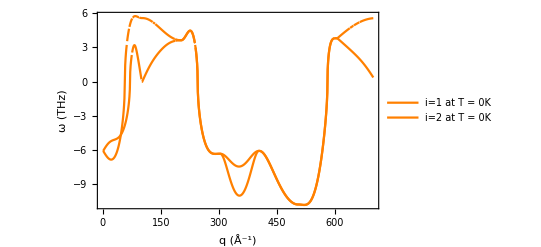

```mathematica
p3=ListLinePlot[Join@@{l1},PlotStyle->Directive[Dashed,Black],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]}];
p3=ListLinePlot[Join@@{l1,l2},PlotStyle->Directive[Orange],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotLegends->{Style["i=1 at T = 0K",18,FontFamily->Times],Style["i=2 at T = 0K",18,FontFamily->Times]}]
```

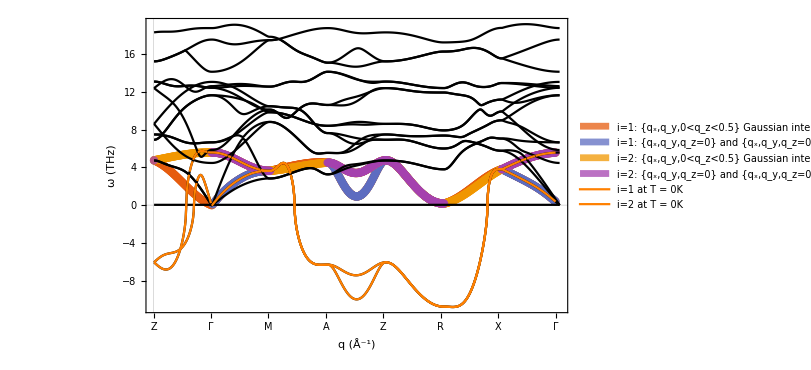

```mathematica
Show[{p1a,p2,p3},ImageSize->600,PlotRange->All]
```

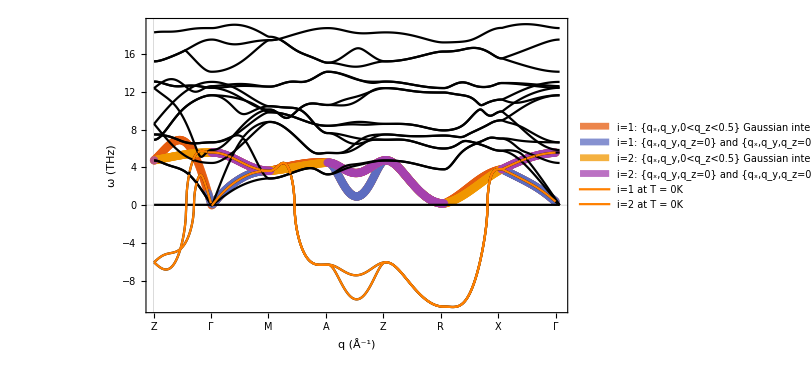

```mathematica
Show[{p1a,p2,p3},ImageSize->600,PlotRange->All]
```